```mathematica
(* set up the Levy alpha-stable SDE *)
α=1;
(* drift *)
(* f[x_] := Sin[x] *)
f[x_]:=x-x^3
(* constant diffusion *)
g=0.25;
```

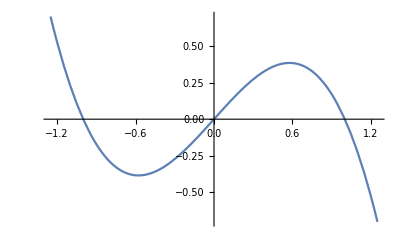

```mathematica
Plot[f[x],{x,-1.25,1.25}]
```

```mathematica
f[x]
```

x-x^3

```mathematica
Integrate[f[x] Exp[-I k x/2],{x,-2 π, 2π}]/(4 π)
```

-(2 ⅈ (k π (-24+k^2 (-1+4 π^2)) Cos[k π]+(24+k^2 (1-12 π^2)) Sin[k π]))/(k^4 π)

```mathematica
FullSimplify[%,k∈Integers]
```

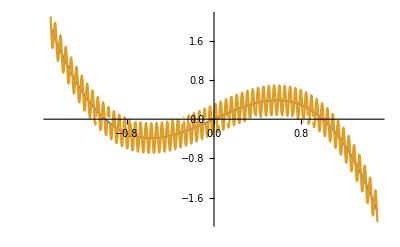

```mathematica
Plot[{x-x^3,Sum[If[k==0,0,-(2 ⅈ (-1)^k (-24+k^2 (-1+4 π^2)))/k^3 ]Exp[I k x/2],{k,-256,256}]},{x,-1.5,1.5}]
```

```mathematica
ntraj=100;
nsamp=1;
plots=Table[{},{i,ntraj}];
numsteps=4000;
tvec=Table[j*dt,{j,0,numsteps}];
dt = 0.001;
ns = numsteps;
For[traj=1,traj≤ntraj,traj+=1,
mcsol=Table[0,ns+1];
mcsol[[1]]=0.0; (* initial condition *)
For[i=1,i≤ns,i+=1,
mcsol[[i+1]] =mcsol[[i]]+ (dt*f[mcsol[[i]]] +  RandomVariate[StableDistribution[1,α,0.0,0.0,(dt)^(1/α) g],nsamp]);
];
fname=StringJoin["mcdblwell1d",ToString[traj],".csv"];
Print[fname];
Export[fname,mcsol];
plots[[traj]]=ListPlot[Transpose[{tvec,Flatten[mcsol]}]]
]
```

mcdblwell1d1.csv

mcdblwell1d2.csv

mcdblwell1d3.csv

mcdblwell1d4.csv

mcdblwell1d5.csv

mcdblwell1d6.csv

mcdblwell1d7.csv

mcdblwell1d8.csv

mcdblwell1d9.csv

mcdblwell1d10.csv

mcdblwell1d11.csv

mcdblwell1d12.csv

mcdblwell1d13.csv

mcdblwell1d14.csv

mcdblwell1d15.csv

mcdblwell1d16.csv

mcdblwell1d17.csv

mcdblwell1d18.csv

mcdblwell1d19.csv

mcdblwell1d20.csv

mcdblwell1d21.csv

mcdblwell1d22.csv

mcdblwell1d23.csv

mcdblwell1d24.csv

mcdblwell1d25.csv

mcdblwell1d26.csv

mcdblwell1d27.csv

mcdblwell1d28.csv

mcdblwell1d29.csv

mcdblwell1d30.csv

mcdblwell1d31.csv

mcdblwell1d32.csv

mcdblwell1d33.csv

mcdblwell1d34.csv

mcdblwell1d35.csv

mcdblwell1d36.csv

mcdblwell1d37.csv

mcdblwell1d38.csv

mcdblwell1d39.csv

mcdblwell1d40.csv

mcdblwell1d41.csv

mcdblwell1d42.csv

mcdblwell1d43.csv

mcdblwell1d44.csv

mcdblwell1d45.csv

mcdblwell1d46.csv

mcdblwell1d47.csv

mcdblwell1d48.csv

mcdblwell1d49.csv

mcdblwell1d50.csv

mcdblwell1d51.csv

mcdblwell1d52.csv

mcdblwell1d53.csv

mcdblwell1d54.csv

mcdblwell1d55.csv

mcdblwell1d56.csv

mcdblwell1d57.csv

mcdblwell1d58.csv

mcdblwell1d59.csv

mcdblwell1d60.csv

mcdblwell1d61.csv

mcdblwell1d62.csv

mcdblwell1d63.csv

mcdblwell1d64.csv

mcdblwell1d65.csv

mcdblwell1d66.csv

mcdblwell1d67.csv

mcdblwell1d68.csv

mcdblwell1d69.csv

mcdblwell1d70.csv

mcdblwell1d71.csv

mcdblwell1d72.csv

mcdblwell1d73.csv

mcdblwell1d74.csv

mcdblwell1d75.csv

mcdblwell1d76.csv

mcdblwell1d77.csv

mcdblwell1d78.csv

mcdblwell1d79.csv

mcdblwell1d80.csv

mcdblwell1d81.csv

mcdblwell1d82.csv

mcdblwell1d83.csv

mcdblwell1d84.csv

mcdblwell1d85.csv

mcdblwell1d86.csv

mcdblwell1d87.csv

mcdblwell1d88.csv

mcdblwell1d89.csv

mcdblwell1d90.csv

mcdblwell1d91.csv

mcdblwell1d92.csv

mcdblwell1d93.csv

mcdblwell1d94.csv

mcdblwell1d95.csv

mcdblwell1d96.csv

mcdblwell1d97.csv

mcdblwell1d98.csv

mcdblwell1d99.csv

mcdblwell1d100.csv